{x[0]==0,θ[0]==0,y[0]==0,F1[1]==0,F2[1]==0,ω[1]==0}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],θ→InterpolatingFunction[…],ω→InterpolatingFunction[…],F1→InterpolatingFunction[…],F2→InterpolatingFunction[…]}}

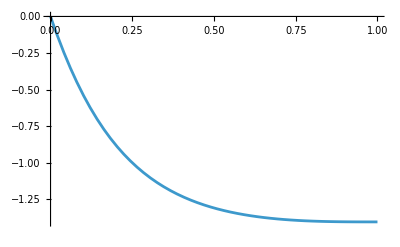

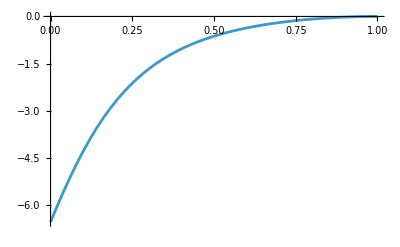

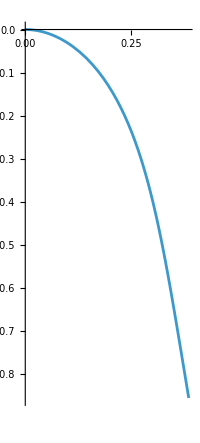

```mathematica
Clear["`*"]
g=50;
B=2;
L=1;
eqns={F1'[s]-ω[s] F2[s]-g Sin[θ[s]]==0,F2'[s]+ω[s] F1[s]-g Cos[θ[s]]==0,B ω'[s]+F2[s]==0,θ'[s]==ω[s],x'[s]==Cos[θ[s]],y'[s]==Sin[θ[s]]};
BC={x[0]==0,θ[0]==0,y[0]==0,F1[L]==0,F2[L]==0,ω[L]==0}
sol=NDSolve[eqns~Join~BC,{x,y,θ,ω,F1,F2},{s,0,L}]
Plot[θ[s]/.sol[[1]],{s,0,L}]
Plot[ω[s]/.sol[[1]],{s,0,L}]
ParametricPlot[{x[s],y[s]}/.sol[[1]],{s,0,L}]
```

```mathematica
ClearAll["Global`*"];
GetSol[L_,g_,B_,R_,ϕc_?NumericQ]:=Module[{eqns,BC,sol},eqns={F1'[s]-ω[s] F2[s]-g Sin[θ[s]]==0,F2'[s]+ω[s] F1[s]-g Cos[θ[s]]==0,B ω'[s]+F2[s]==0,θ'[s]==ω[s],x'[s]==Cos[θ[s]],y'[s]==Sin[θ[s]]};
BC={x[0]==R Sin[ϕc],y[0]==R Cos[ϕc],θ[0]==-ϕc,F1[L-R ϕc]==0,F2[L-R ϕc]==0,ω[L-R ϕc]==0};
sol=NDSolve[Join[eqns,BC],{x,y,θ,ω,F1,F2},{s,0,L-R ϕc}];
sol]

GetResidual[L_,g_,B_,R_,ϕc_?NumericQ]:=Module[{sol},sol=GetSol[L,g,B,R,ϕc];
((F1[s]/. sol[[1]]/. s->0)-g R Cos[ϕc])]
```

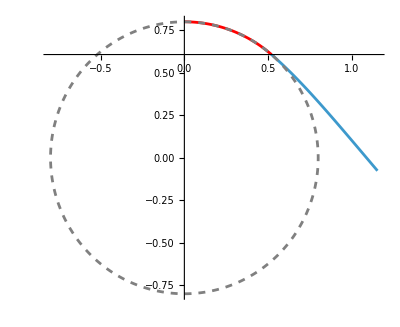

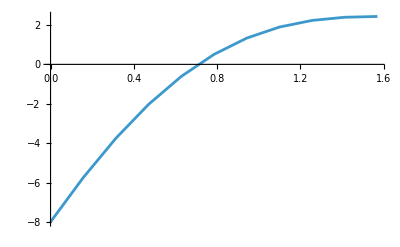

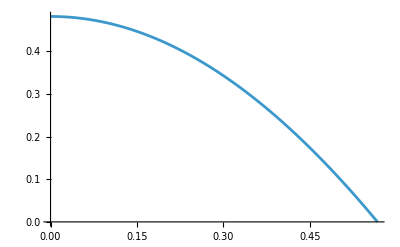

0.180578

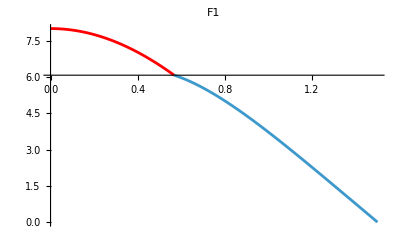

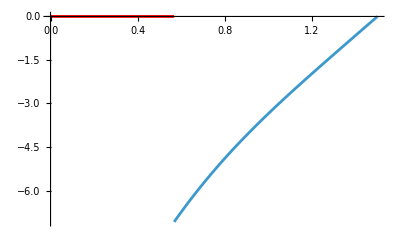

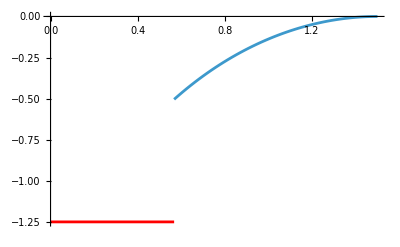

7.26258

0.180578

```mathematica
R=0.8;
L=1.5;
B=6;
g=10;
ϕc=ϕcp/.FindRoot[GetResidual[L,g,B,R,ϕcp],{ϕcp,π/4}][[1]];
sol=GetSol[L,g,B,R,ϕc];

Show[{ParametricPlot[{R Sin[s/R],R Cos[s/R]},{s,0,R ϕc},PlotStyle->Red,PlotRange->All,AspectRatio->Automatic],ParametricPlot[Evaluate[{x[s],y[s]}/. sol[[1]]],{s,0,L-R ϕc},PlotRange->All],ParametricPlot[{R Sin[s/R],R Cos[s/R]},{s,0,2 π R},PlotStyle->{Dashed,Gray},PlotRange->All]}]

ListLinePlot[Transpose[{Range[0,π/2,π/20],GetResidual[L,g,B,R,#]&/@Range[0,π/2,π/20]}],PlotRange->Full]

Plot[2(Cos[s/R]-Cos[ϕc]),{s,0,R ϕc}]
NIntegrate[2(Cos[s/R]-Cos[ϕc]),{s,0,R ϕc}]
Show[{Plot[R g(Cos[s/R]) ,{s,0,ϕc R},PlotLabel->"F1",PlotStyle->Red,PlotRange->All],Plot[F1[s-ϕc R]/.sol[[1]],{s,ϕc R,L}]}]
Show[{Plot[0 ,{s,0,ϕc R},PlotStyle->Red,PlotRange->All],Plot[F2[s-ϕc R]/.sol[[1]],{s,ϕc R,L}]}]
Show[{Plot[-1/R ,{s,0,ϕc R},PlotStyle->Red,PlotRange->All],Plot[ω[s-ϕc R]/.sol[[1]],{s,ϕc R,L}]}]

NIntegrate[2(Cos[s/R]-Cos[ϕc]),{s,0,R ϕc}]-F2[s]/.sol[[1]]/.{s->0}
NIntegrate[2(Cos[s/R]-Cos[ϕc]),{s,0,R ϕc}]
```

```mathematica
LArray=Range[0.9,3,2.1/20];
RArray=Range[0.5,2,2.1/20];
R=0.5;
L=3;
B=6;
g=10;

Pre=Table[0,{i,1,21},{j,1,21}];
Do[
R=RArray[[i]];
L=LArray[[j]];
ϕc=ϕcp/.FindRoot[GetResidual[L,g,B,R,ϕcp],{ϕcp,π/4}][[1]];
sol=GetSol[L,g,B,R,ϕc];
Pre[[i,j]]=NIntegrate[2(Cos[s/R]-Cos[ϕc]),{s,0,R ϕc}]-F2[s]/.sol[[1]]/.{s->0};
Print[Pre[[i,j]]]
,{i,1,21},{j,1,21}]
```

3.83258

5.69

7.29054

8.75175

10.1249

11.4374

12.7058

13.941

15.1504

16.3391

17.5112

18.6694

19.8162

20.9532

22.082

23.2036

24.319

NDSolve::berr: 762320. 的标量边界值残差表明边界值不满足指定的容差. 返回求得的最佳解.

General::stop: 在本次计算中，NDSolve::berr 的进一步输出将被抑制.

25.429

26.5343

27.6354

28.7327

4.79743

2.77072

5.04226

6.8679

8.48455

9.97586

11.3831

12.7302

14.0321

15.299

16.5381

17.7548

18.9529

20.1355

21.3049

22.4632

23.6119

24.7521

25.885

27.0115

28.1323

9.81683

7.28317

2.64411

4.11269

6.24053

8.04579

9.67443

11.1893

12.6245

14.0006

15.3313

16.6262

17.8921

19.1341

20.3562

21.5615

22.7524

23.9309

FindRoot::sszero: 搜索中的步长比由 PrecisionGoal 选项规定的容差小，但是函数值仍然大于由 AccuracyGoal 选项规定的容差.

25.0986

26.2569

27.4069

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

13.8238

11.8483

FindRoot::cvmit: 无法在 100 次迭代中收敛到要求的准确度或者精度.

General::stop: 在本次计算中，FindRoot::cvmit 的进一步输出将被抑制.

NDSolve::ndsz: 在 s == -2.40741×10^-35 处，步长实际上为零；可能存在奇点或者刚性系统.

NDSolve::ndsz: 在 s == -9.62965×10^-35 处，步长实际上为零；可能存在奇点或者刚性系统.

General::stop: 在本次计算中，NDSolve::ndsz 的进一步输出将被抑制.

9.51512

6.36384

2.79108

5.38817

7.43261

9.22367

10.8616

12.3955

13.8538

15.2547

16.6106

17.9301

19.22

20.4851

21.7293

22.9557

24.1666

25.3643

26.5502

17.5583

15.7973

13.8606

11.6475

8.91908

4.56434

4.25806

6.6316

8.62095

10.4015

12.0468

13.5964

15.0743

16.4966

17.8744

19.216

20.5275

21.8136

23.0781

24.324

25.5538

$Aborted

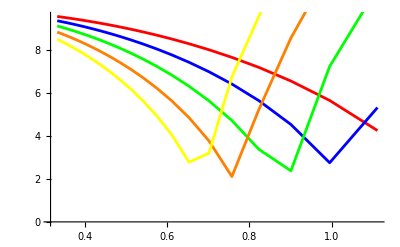

```mathematica
Show[{ListLinePlot[Transpose[{1/LArray,Pre[[1,;;]]/LArray}],PlotRange->All,PlotStyle->Red],ListLinePlot[Transpose[{1/LArray,Pre[[2,;;]]/LArray}],PlotRange->All,PlotStyle->Blue],ListLinePlot[Transpose[{1/LArray,Pre[[3,;;]]/LArray}],PlotRange->All,PlotStyle->Green],ListLinePlot[Transpose[{1/LArray,Pre[[4,;;]]/LArray}],PlotRange->All,PlotStyle->Orange],ListLinePlot[Transpose[{1/LArray,Pre[[5,;;]]/LArray}],PlotRange->All,PlotStyle->Yellow]}]
```

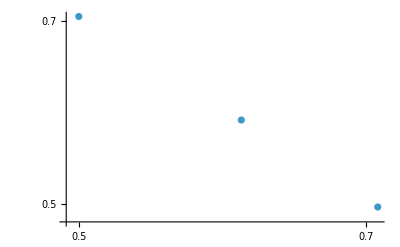

-0.999995

-1.00001

-1.

```mathematica
p0=8;
f1=Interpolation[Transpose[{Pre[[1,;;]]/(LArray),1/LArray}]];
f2=Interpolation[Transpose[{Pre[[2,;;]]/(LArray),1/LArray}]];
f3=Interpolation[Transpose[{Pre[[3,;;]]/(LArray),1/LArray}]];
ListLogLogPlot[Transpose[{RArray[[1;;3]],{f1[p0],f2[p0],f3[p0]}}]]
(*Transpose[{RArray[[1;;3]],{f1[0.1],f2[0.1],f3[0.1]}}]*)

mode={f1[p0],f2[p0],f3[p0]};
Ra=RArray;
Log[mode[[1]]/mode[[2]]]/Log[Ra[[1]]/Ra[[2]]]
Log[mode[[2]]/mode[[3]]]/Log[Ra[[2]]/Ra[[3]]]
Log[mode[[1]]/mode[[3]]]/Log[Ra[[1]]/Ra[[3]]]
```

```mathematica
Pre
```

{{0.143992,0.078442,0.049821,0.0343283,0.0249344,0.018808,0.0146005,0.0115956,0.00938245,0.00771094,0.00642186,0.00540992,0.0046033,0.00395173,0.00341918,0.00297934,0.00261267,0.0023044,0.00204325,0.00182047,0.0016292},{2.47739,0.322991,0.154902,0.0953174,0.064995,0.0470801,0.0355349,0.027647,0.0220231,0.0178795,0.0147453,0.0123229,0.0104164,0.0088925,0.00765795,0.00664596,0.00580774,0.00510695,0.00451615,0.0040143,0.00358506},{3.54505,3.20686,2.08675,0.291922,0.168204,0.112195,0.0805629,0.0606146,0.0471377,0.0375847,0.0305657,0.0252615,0.021161,0.0179308,0.0153452,0.013247,0.0115238,0.0100937,0.0088956,0.00788348,0.00702196},{4.31201,4.13124,3.85242,3.31688,0.581004,0.285181,0.182699,0.129073,0.0964026,0.0747298,0.0595245,0.0484181,0.0400528,0.0335965,0.0285134,0.0244441,0.0211398,0.0184235,0.0161665,0.0142732,0.0126715},{5.01012,4.88296,4.71225,4.46753,4.07019,3.08964,0.485724,0.28784,0.197875,0.145952,0.112438,0.089287,0.0725344,0.0599884,0.0503395,0.0427581,0.0366953,0.031774,0.0277282,0.024365,0.0215419},{5.67987,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/mnt/Materials/00_MyWebsite/lijh0417.github.io/_posts